```mathematica
ReportOnMatrix[m_]:=Block[{diamond=m[[1,2,1]],result={-1,-1,-1,-1,-1,-1}, real={m[[1,3]],m[[1,4]],m[[2,4]],m[[2,5]],m[[3,5]]}},

result[[1]]=Length[Select[real,#==diamond&]];
result[[2]]=Length[Select[real,#==diamond*3/4&]];
result[[3]]=Length[Select[real,#==diamond/2&]];
result[[4]]=Length[Select[real,#>=diamond&]];
result[[5]]=Length[Select[real,#>=diamond*3/4&]];
result[[6]]=Length[Select[real,#>=diamond/2&]];
result]
```

```mathematica
EdgeDelete
```

```mathematica
AdjacencyMatrix[Graph[{1<->2,1<->2}]]
```

SparseArray[<2>, {2, 2}]

```mathematica
CycleEdges[vertices_]:=Join[Table[vertices[[i]]<->vertices[[i+1]],{i,1,Length[vertices]-1}],{vertices[[Length[vertices]]]<->vertices[[1]]}]
```

```mathematica
CycleEdges[{1,2,3}]
```

{1<->2,2<->3,3<->1}

```mathematica
MyEdgeDelete[g_,edges_]:=Block[{mat},
mat=AdjacencyMatrix[g];
Table[With[{
i=VertexIndex[g,e[[1]]],
j=VertexIndex[g,e[[2]]]},
mat[[i,j]]--;
mat[[j,i]]--
]
,{e,edges}
];
AdjacencyGraph[VertexList[g],mat]
]
```

```mathematica
DistanceMatrix[g_, vertices_] := Table[With[{p=FindShortestPath[g,v1,v2]},If[p=={},-1,Length[p]]],{v1,vertices},{v2,vertices}]
```

```mathematica
deps3=ReadList["D:\\Grofs\\dependencies3.txt",Expression];Length[deps3]
```

2436995

```mathematica
PathMatrix[g_, vertices_] := Table[FindShortestPath[g,v1,v2],{v1,vertices},{v2,vertices}]
```

```mathematica
Sort[Tally[Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=MyEdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
{ReportOnMatrix[GenMatrix[g,record[[3,2]]]], MatrixForm[DistanceMatrix[g,record[[3,2]]]]}
]
],
{k,1,100}
],
k]]]
```

{{{{0,0,0,0,0,5},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},7},{{{0,0,0,0,2,4},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},12},{{{0,0,0,0,3,3},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},2},{{{0,2,1,0,4,5},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},2},{{{1,0,0,1,2,4},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},1},{{{1,0,0,1,3,3},(1 | 2 | 2 | 3 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},13},{{{1,0,0,1,3,3},(1 | 2 | 3 | 2 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
2 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},5},{{{1,0,0,1,3,3},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},7},{{{1,0,0,1,3,4},(1 | 2 | 2 | 3 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},6},{{{1,0,0,1,3,4},(1 | 2 | 3 | 2 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
2 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},5},{{{1,0,0,1,3,4},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},3},{{{2,1,2,2,3,5},(1 | 2 | 2 | 2 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 3
2 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},25},{{{2,1,2,2,3,5},(1 | 2 | 2 | 3 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},12}}

```mathematica
s
```

```mathematica
Det[({{1, 2, 3, 3, 2}, {2, 1, 2, 3, 3}, {3, 2, 1, 2, 3}, {3, 3, 2, 1, 2}, {2, 3, 3, 2, 1}})]
```

11

```mathematica
MatrixForm[Mod[({{1, 2, 3, 3, 2}, {2, 1, 2, 3, 3}, {3, 2, 1, 2, 3}, {3, 3, 2, 1, 2}, {2, 3, 3, 2, 1}}),2]]
```

(1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1)

```mathematica
Det[({{1, 0, 1, 1, 0}, {0, 1, 0, 1, 1}, {1, 0, 1, 0, 1}, {1, 1, 0, 1, 0}, {0, 1, 1, 0, 1}})]
```

3

```mathematica
MatrixForm[Mod[({{1, 2, 2, 2, 2}, {2, 1, 2, 3, 3}, {2, 2, 1, 2, 3}, {2, 3, 2, 1, 2}, {2, 3, 3, 2, 1}}),2]]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 1)

```mathematica
Det[({{1, 0, 0, 0, 0}, {0, 1, 0, 1, 1}, {0, 0, 1, 0, 1}, {0, 1, 0, 1, 0}, {0, 1, 1, 0, 1}})]
```

-1

```mathematica
Det[({{1, 0, 0, 1, 0}, {0, 1, 0, 1, 1}, {0, 0, 1, 0, 0}, {1, 1, 0, 1, 0}, {0, 1, 0, 0, 1}})]
```

-1

```mathematica
MatrixForm[Mod[({{1, 2, 2, 3, 2}, {2, 1, 2, 3, 3}, {2, 2, 1, 2, 2}, {3, 3, 2, 1, 2}, {2, 3, 2, 2, 1}}),2]]
```

(1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 1
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1)

```mathematica
N[Style[1,Black]]
```

1.

```mathematica
Sort[Tally[Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=MyEdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
{ReportOnMatrix[GenMatrix[g,record[[3,2]]]], MatrixForm[DistanceMatrix[g,record[[3,2]]]]}
]
],
{k,1,100}
],
k]]]
```

{{{{0,0,0,0,0,5},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},7},{{{0,0,0,0,2,4},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},12},{{{0,0,0,0,3,3},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},2},{{{0,2,1,0,4,5},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},2},{{{1,0,0,1,2,4},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},1},{{{1,0,0,1,3,3},(1 | 2 | 2 | 3 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},13},{{{1,0,0,1,3,3},(1 | 2 | 3 | 2 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
2 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},5},{{{1,0,0,1,3,3},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},7},{{{1,0,0,1,3,4},(1 | 2 | 2 | 3 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 3
3 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},6},{{{1,0,0,1,3,4},(1 | 2 | 3 | 2 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 3
2 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},5},{{{1,0,0,1,3,4},(1 | 2 | 3 | 3 | 2
2 | 1 | 2 | 3 | 3
3 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},3},{{{2,1,2,2,3,5},(1 | 2 | 2 | 2 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 3
2 | 3 | 2 | 1 | 2
2 | 3 | 3 | 2 | 1)},25},{{{2,1,2,2,3,5},(1 | 2 | 2 | 3 | 2
2 | 1 | 2 | 3 | 3
2 | 2 | 1 | 2 | 2
3 | 3 | 2 | 1 | 2
2 | 3 | 2 | 2 | 1)},12}}

```mathematica
{{{2,1,2,2,3,5},2774},{{1,0,0,1,3,3},1511},{{0,0,0,0,0,5},718},{{0,0,0,0,2,4},1643},{{1,0,0,1,3,4},1050},{{0,0,0,0,3,3},465},{{1,0,0,1,2,4},473},{{0,2,1,0,4,5},216},{{1,0,0,1,2,5},485},{{0,1,2,0,1,5},77},{{1,1,1,1,3,4},112},{{0,0,0,0,2,5},132},{{0,0,1,0,2,5},68},{{1,2,0,1,3,5},37},{{0,0,0,0,1,3},11},{{1,1,0,1,3,4},12},{{0,0,0,0,3,5},12},{{0,0,1,0,3,5},12},{{1,0,0,1,1,5},27},{{0,0,0,0,3,4},77},{{0,1,0,0,4,4},14},{{0,0,0,0,2,3},7},{{0,0,1,0,3,4},11},{{0,0,0,0,0,4},10},{{0,2,1,0,2,5},5},{{0,2,0,0,4,4},5},{{0,0,0,0,4,4},9},{{0,2,0,0,3,5},9},{{0,0,0,0,1,5},5},{{0,0,1,0,2,4},3},{{1,1,1,1,2,5},4},{{0,1,2,0,3,5},3},{{0,1,0,0,3,5},1},{{0,2,0,0,4,5},1},{{0,1,0,0,3,3},1}}
```

```mathematica
FindShortestPath
```

```mathematica
{{{2,1,2},2774},{{1,0,0},3546},{{0,0,0},3089},{{0,2,1},221},{{0,1,2},80},{{1,1,1},116},{{0,0,1},94},{{1,2,0},37},{{1,1,0},12},{{0,1,0},16},{{0,2,0},15}}
```

```mathematica
Sort[
Tally[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=EdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
GenMatrix[g,record[[3,2]]][[6,6]]/2
]
],
{k,1,100000}
],
k]
]
]
```

Tally::list: List expected at position 1 in Tally[$Aborted].

Tally[$Aborted]

```mathematica
{{6,299},{190/31,4},{25/4,48},{120/19,2},{70/11,137},{110/17,66},{150/23,3},{46/7,2},{20/3,1107},{115/17,21},{75/11,42},{130/19,41},{55/8,57},{90/13,47},{7,538},{190/27,8},{120/17,9},{85/12,12},{50/7,699},{115/16,1},{65/9,13},{80/11,4},{95/13,51},{22/3,42},{170/23,31},{15/2,1716}}
```

```mathematica
{{6,299},{190/31,4},{25/4,48},{120/19,2},{70/11,137},{110/17,66},{150/23,3},{46/7,2},{20/3,1107},{115/17,21},{75/11,42},{130/19,41},{55/8,57},{90/13,47},{7,538},{190/27,8},{120/17,9},{85/12,12},{50/7,699},{115/16,1},{65/9,13},{80/11,4},{95/13,51},{22/3,42},{170/23,31},{15/2,1716}}
```

```mathematica
Tally[
Map[{Chrom[#[[1]]],Chrom[#[[2]]]}/24&,
Select[
Take[deps3,10000],With[
{g=EdgeDelete[ReadGrof[#[[1]]],#[[3,3]]]},
GenMatrix[g,#[[3,2]]][[6,6]]==15/2
]&
]
]
]
```

{{{1,1},2018},{{5,2},90},{{4,4},391},{{4,2},39},{{3,3},261},{{3,2},102},{{4,3},98},{{5,5},273},{{5,3},136},{{2,2},25},{{6,5},2},{{12,12},17},{{9,7},5},{{21,11},1},{{21,6},1},{{11,11},2},{{11,4},1},{{11,6},2},{{9,5},3},{{9,6},1},{{7,4},6},{{7,7},11},{{7,6},2},{{9,4},1},{{12,11},2},{{12,4},1},{{12,7},5},{{12,6},1},{{6,4},1},{{9,9},14},{{20,7},1},{{20,8},2},{{6,6},10},{{25,8},1},{{13,5},1},{{11,5},1},{{11,7},1},{{5,4},2}}

```mathematica
SortBy[%389,Last]
```

{{{6,4},1},{{9,4},1},{{9,6},1},{{11,4},1},{{11,5},1},{{11,7},1},{{12,4},1},{{12,6},1},{{13,5},1},{{20,7},1},{{21,6},1},{{21,11},1},{{25,8},1},{{5,4},2},{{6,5},2},{{7,6},2},{{11,6},2},{{11,11},2},{{12,11},2},{{20,8},2},{{9,5},3},{{9,7},5},{{12,7},5},{{7,4},6},{{6,6},10},{{7,7},11},{{9,9},14},{{12,12},17},{{2,2},25},{{4,2},39},{{5,2},90},{{4,3},98},{{3,2},102},{{5,3},136},{{3,3},261},{{5,5},273},{{4,4},391},{{1,1},2018}}

```mathematica
SortBy[%389,Last]
```

{{{6,4},1},{{9,4},1},{{9,6},1},{{11,4},1},{{11,5},1},{{11,7},1},{{12,4},1},{{12,6},1},{{13,5},1},{{20,7},1},{{21,6},1},{{21,11},1},{{25,8},1},{{5,4},2},{{6,5},2},{{7,6},2},{{11,6},2},{{11,11},2},{{12,11},2},{{20,8},2},{{9,5},3},{{9,7},5},{{12,7},5},{{7,4},6},{{6,6},10},{{7,7},11},{{9,9},14},{{12,12},17},{{2,2},25},{{4,2},39},{{5,2},90},{{4,3},98},{{3,2},102},{{5,3},136},{{3,3},261},{{5,5},273},{{4,4},391},{{1,1},2018}}

```mathematica
{{{1,1},288},{{5,2},8},{{4,4},24},{{4,2},6},{{3,3},16},{{3,2},6},{{4,3},13},{{5,5},5},{{5,3},11},{{2,2},2}}
```

```mathematica
vals=Map[First[#]&,{{{1,1},2018},{{5,2},90},{{4,4},391},{{4,2},39},{{3,3},261},{{3,2},102},{{4,3},98},{{5,5},273},{{5,3},136},{{2,2},25},{{6,5},2},{{12,12},17},{{9,7},5},{{21,11},1},{{21,6},1},{{11,11},2},{{11,4},1},{{11,6},2},{{9,5},3},{{9,6},1},{{7,4},6},{{7,7},11},{{7,6},2},{{9,4},1},{{12,11},2},{{12,4},1},{{12,7},5},{{12,6},1},{{6,4},1},{{9,9},14},{{20,7},1},{{20,8},2},{{6,6},10},{{25,8},1},{{13,5},1},{{11,5},1},{{11,7},1},{{5,4},2}}]
```

{{1,1},{5,2},{4,4},{4,2},{3,3},{3,2},{4,3},{5,5},{5,3},{2,2},{6,5},{12,12},{9,7},{21,11},{21,6},{11,11},{11,4},{11,6},{9,5},{9,6},{7,4},{7,7},{7,6},{9,4},{12,11},{12,4},{12,7},{12,6},{6,4},{9,9},{20,7},{20,8},{6,6},{25,8},{13,5},{11,5},{11,7},{5,4}}

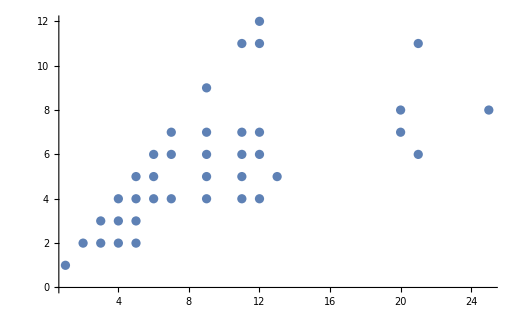

```mathematica
ListPlot[vals, PlotRange->All]
```

```mathematica
a=Map[First[#]&,{{3,692},{95/31,10},{115/37,1},{25/8,77},{60/19,3},{35/11,271},{55/17,127},{13/4,4},{75/23,10},{95/29,6},{23/7,3},{155/47,1},{10/3,2039},{115/34,36},{95/28,3},{17/5,7},{75/22,85},{65/19,100},{55/16,114},{100/29,5},{45/13,128},{80/23,1},{185/53,1},{7/2,1072},{165/47,1},{95/27,21},{60/17,22},{85/24,29},{135/38,1},{25/7,1335},{115/32,7},{65/18,33},{185/51,1},{40/11,13},{95/26,85},{11/3,72},{125/34,6},{70/19,4},{85/23,43},{15/4,3531}}]
```

{3,95/31,115/37,25/8,60/19,35/11,55/17,13/4,75/23,95/29,23/7,155/47,10/3,115/34,95/28,17/5,75/22,65/19,55/16,100/29,45/13,80/23,185/53,7/2,165/47,95/27,60/17,85/24,135/38,25/7,115/32,65/18,185/51,40/11,95/26,11/3,125/34,70/19,85/23,15/4}

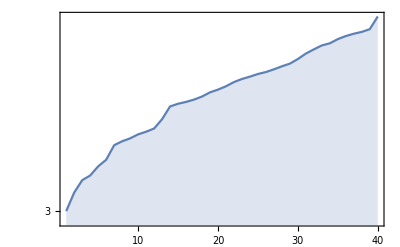

```mathematica
ListLogPlot[a, Filling->Axis, Joined->True,PlotRange->All, GridLines->Automatic, Frame->True]
```

```mathematica
GenMatrix123[g_,vertices_,n_]:=Block[
{result=Table[-1,{i,1,6},{j,1,6}],i,j, v1, v2, graph2,vert, div},
For[i=1,i≤5,i++,
v1=vertices[[i]];
For[j=1,j≤i,j++,
v2=vertices[[j]];
If[i==j,
vert={v1<->vertices[[Mod[i+1,5]+1]],v1<->vertices[[Mod[i+2,5]+1]]};
graph2=EdgeAdd[g,vert];
result[[i,j]]=ChromaticPolynomial[graph2,n]
,
graph2=EdgeAdd[g,v1<->v2];
result[[i,j]]=ChromaticPolynomial[graph2,n];
result[[j,i]]=result[[i,j]]
]
];
];
div=result[[1,2]];
For[i=1,i≤5,i++,
result[[i,6]]=Sum[result[[i,k]],{k,1,5}]-result[[i,i]]-2*result[[i,Mod[i,5]+1]];
result[[6,i]]=Sum[result[[k,i]],{k,1,5}]-result[[i,i]]-2*result[[Mod[i,5]+1,i]];
];

result[[6,6]]=Sum[result[[6,k]],{k,1,5}]/div;
For[i=1,i≤5,i++,
result[[i,i]]=Style[result[[i,i]],Bold, Red];
result[[i,Mod[i,5]+1]]=Style[result[[i,Mod[i,5]+1]],Italic, Blue];
result[[i,Mod[i+3,5]+1]]=Style[result[[i,Mod[i+3,5]+1]],Italic,Blue];
];
result]
```

```mathematica
Sort[
Tally[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=EdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
GenMatrix123[g,record[[3,2]]][[6,6]]
]
],
{k,1,1000}
],
k]
]
]
```

{{7,80},{36/5,25},{992/137,3},{922/127,6},{2494/339,3},{449/61,4},{193/26,14},{958/129,31},{172/23,92},{158/21,208},{2026/269,3},{425/56,1},{137/18,1},{130/17,102},{23/3,4},{882/115,22},{868/113,3},{559/72,3},{320/41,5},{932/119,3},{496/63,5},{197/25,20},{214/27,3},{454/57,40},{898/111,2},{74/9,317}}

```mathematica
With[
{n=5},
Sort[
Tally[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=EdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
GenMatrix123[g,record[[3,2]],n][[6,6]]
]
],
{k,1,1000}
],
k]
]
]
]
```

{{7,80},{36/5,25},{992/137,3},{922/127,6},{2494/339,3},{449/61,4},{193/26,14},{958/129,31},{172/23,92},{158/21,208},{2026/269,3},{425/56,1},{137/18,1},{130/17,102},{23/3,4},{882/115,22},{868/113,3},{559/72,3},{320/41,5},{932/119,3},{496/63,5},{197/25,20},{214/27,3},{454/57,40},{898/111,2},{74/9,317}}

```mathematica
With[
{n=6},
Sort[
Tally[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=EdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
GenMatrix123[g,record[[3,2]],n][[6,6]]
]
],
{k,1,1000}
],
k]
]
]
]
```

{{130/17,80},{4682/607,3},{1402/181,25},{4526/579,4},{2292/293,6},{1396/177,14},{434/55,92},{7881/998,3},{246/31,5},{375/47,3},{1158/145,26},{2233/279,1},{2208/275,22},{4424/549,1},{4982/617,3},{105/13,208},{699/86,102},{1130/139,3},{4694/577,5},{163/20,4},{710/87,20},{1163/142,3},{58/7,5},{1113/134,3},{765/92,40},{1179/140,2},{69/8,317}}

```mathematica
With[
{n=7},
Sort[
Tally[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=EdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
GenMatrix123[g,record[[3,2]],n][[6,6]]
]
],
{k,1,1000}
],
k]
]
]
]
```

{{105/13,80},{1448/179,3},{3748/461,25},{7857/962,4},{15838/1933,6},{896/109,92},{625/76,14},{16022/1937,5},{64494/7777,3},{13678/1649,3},{7841/944,1},{15406/1853,22},{8263/991,3},{869/104,1},{5314/635,26},{16088/1917,5},{1899/226,20},{15824/1881,3},{886/105,208},{16048/1901,3},{3766/445,102},{2077/245,4},{4156/485,5},{68494/7985,3},{266/31,40},{3282/379,2},{222/25,317}}

```mathematica
With[
{n=8},
Sort[
Tally[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=EdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
GenMatrix123[g,record[[3,2]],n][[6,6]]
]
],
{k,1,1000}
],
k]
]
]
]
```

{{43298/5171,3},{310/37,80},{8334/991,25},{43042/5105,4},{10819/1279,6},{1618/191,92},{8348/985,14},{43606/5121,5},{109343/12823,3},{21551/2525,1},{21198/2483,22},{44354/5187,3},{14364/1675,1},{113783/13263,3},{14586/1697,5},{43/5,20},{10852/1259,3},{21874/2533,3},{21788/2523,26},{808/93,208},{1401/161,102},{4495/516,4},{4502/513,5},{114343/13023,3},{4373/498,40},{11191/1266,2},{163/18,317}}

```mathematica
Table[
{n,First[
First[Sort[
Tally[
Monitor[

Table[
With[{record=deps3[[k]]},
With[
{g=EdgeDelete[ReadGrof[record[[1]]],record[[3,3]]]},
GenMatrix123[g,record[[3,2]],n][[6,6]]
]
],
{k,1,1000}
],
k]
]
]]]},
{n,4,20}
]
```

{{4,6},{5,7},{6,130/17},{7,105/13},{8,43298/5171},{9,100400/11689},{10,207082/23647},{11,390632/43937},{12,686978/76339},{13,1141888/125641},{14,1812170/197759},{15,2766872/299857},{16,4088482/440467},{17,5874128/629609},{18,748798/79901},{19,11306440/1201729},{20,15231362/1613267}}

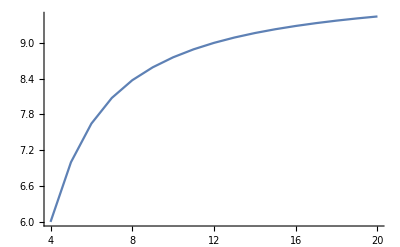

```mathematica
ListPlot[{{4,6},{5,7},{6,130/17},{7,105/13},{8,43298/5171},{9,100400/11689},{10,207082/23647},{11,390632/43937},{12,686978/76339},{13,1141888/125641},{14,1812170/197759},{15,2766872/299857},{16,4088482/440467},{17,5874128/629609},{18,748798/79901},{19,11306440/1201729},{20,15231362/1613267}}, Joined->True]
```

```mathematica
FromContinuedFraction[{6,7,130/17,105/13,43298/5171,100400/11689}]
```

2714525570231497/442085144833158

```mathematica
N[{{4,6},{5,7},{6,130/17},{7,105/13},{8,43298/5171},{9,100400/11689},{10,207082/23647},{11,390632/43937},{12,686978/76339},{13,1141888/125641},{14,1812170/197759},{15,2766872/299857},{16,4088482/440467},{17,5874128/629609},{18,748798/79901},{19,11306440/1201729},{20,15231362/1613267}}]
```

{{4.,6.},{5.,7.},{6.,7.64706},{7.,8.07692},{8.,8.37324},{9.,8.58927},{10.,8.75722},{11.,8.89073},{12.,8.99904},{13.,9.0885},{14.,9.16353},{15.,9.22731},{16.,9.28215},{17.,9.3298},{18.,9.37157},{19.,9.40848},{20.,9.44132}}

```mathematica
$HistoryLength=1
```

1